## 2 RG&TC-Code

version 3.5.1 - June 2007

```mathematica
Off[General::"spell",General::"spell1",UpSet::"write"];
```

```mathematica
If[d[0]=!=0,Unprotect["Global`*"];ClearAll["Global`*"];Remove["Global`*"];Unprotect[In,Out];Clear[In,Out];Protect[In,Out];$Line=0;$RecursionLimit=256;$IterationLimit=4096;Unprotect[SeriesData];If[$VersionNumber<5,Times[x_SeriesData,0]^=0];SeriesData[x1_,x2_,x3_,x4_,x5_,x6_]:= Plus@@If[x2===Infinity,Map[First[#]/x1^((x4+Last[#]-1)/x6)&,Transpose[{x3,Range[Length[x3]]}]]+SeriesData[x1,x2,{},x4,x5,x6],   Map[First[#]*(x1-x2)^((x4+Last[#]-1)/x6)&,Transpose[{x3,Range[Length[x3]]}]]+SeriesData[x1,x2,{},x4,x5,x6]]/;!FreeQ[x3,x1];Protect[SeriesData];];
```

```mathematica
TrigRules={Cos[θ_]^2*(x_.)+(x_.)*Sin[θ_]^2 ->x,Cot[θ_]^2*(x_.)+Csc[θ_]^2*(y_.):>y/;x+y===0};$RGTCversion=351;FreeALLQ[x_,y_List]:=And@@(FreeQ[x,#1]&)/@y;varList={};simpRules={};
```

```mathematica
SetAttributes[FaSi,{Listable}];FaSi[0]=0;FaSi[x_SeriesData]:=(x/.x[[3]]->FaSi[x[[3]]]);FaSi[x_]:=(#1/.simpRules&)/@If[varList==={}||FreeALLQ[x,varList],Factor[x/.simpRules]/.simpRules,Collect[x/.simpRules,varList,Factor]/.simpRules];
```

```mathematica
SetAttributes[FacSimp,{Listable}];FacSimp[0]=0;FacSimp[x_Equal]:=Equal[FacSimp[First[x]-x[[2]]],0];FacSimp[x_Rule]:=Rule[First[x],FacSimp[x[[2]]]];FacSimp[x_SeriesData]:=(x/.x[[3]]->FacSimp[x[[3]]]);FacSimp[x_]:=(ReplaceAll[#,simpRules]&/@Collect[x/.simpRules,FormVars,FacSimp])/;FormDegree[x]>0;FacSimp[x_]:=(#1/.simpRules&)/@If[varList==={}||FreeALLQ[x,varList],Factor[x/.simpRules]/.simpRules,Collect[x/.simpRules,varList,Factor]/.simpRules];
```

```mathematica
zeroQ[0]=True;zeroQ[x_List]:=And@@(zeroQ/@Union[Flatten[x]]);zeroQ[x_SeriesData]:=If[x[[3]]==={},True,False];zeroQ[x_]:=False;
```

```mathematica
nonZeroL[x_]:=Select[Union[Flatten[{x}]],!zeroQ[#]&]
```

```mathematica
nonZeroN[x_]:=Length[Select[Flatten[{x}],!zeroQ[#]&]]
```

```mathematica
indepTerms[x_,opt_:{}]:=redPlus[redTimes[nonZeroL[x],opt]];
```

```mathematica
redTimes[x_,opt_:{}]:=Block[{tmp$=Select[x,Head[#1]===Times &],rst$},rst$=Complement[x,tmp$]; Union[rst$,Map[numb2[#,opt]&,tmp$]]]
```

```mathematica
numb1[x_,opt_:{}]:=1/;NumericQ[x];numb1[x_^y_.,opt_:{}]:=1/;MemberQ[opt,x];numb1[x_,opt_:{}]:=x;numb2[x_,opt_:{}]:=Times@@Map[numb1[#,opt]&,Level[x,1]]
```

```mathematica
redPlus[x_]:=Block[{tmp$=Select[x,Head[#]===Plus&],rst$,i$,negi$},rst$=Complement[x,tmp$];i$=1;While[i$<Length[tmp$],negi$=Select[tmp$,#===-tmp$[[i$]]&];If[negi$=!={},tmp$=Complement[tmp$,negi$]];i$=i$+1];Union[tmp$,rst$]];
```

```mathematica
RiemSym[h_]:=(h[a_,a_,c_,d_]=0;h[a_,b_,c_,c_]=0;h[a_,b_,c_,d_]:=-h[b,a,c,d]/;a>b;h[a_,b_,c_,d_]:=-h[a,b,d,c]/;c>d;h[a_,b_,c_,d_]:=h[c,d,a,b]/;a>c||(a===c&&b>d));
```

```mathematica
epsilon[a__]:=Signature[{a}];
```

```mathematica
zeroTensor[rnk_]:=Fold[Table,0,List/@Table[Dim,{rnk}]];
```

```mathematica
FuncRepRules[f_[y__],g_,ord_:2]:=FuncRepRules[f[y],g,ord]=Block[{tmp$={f[y]->g},indL=indexList[Length[{y}],ord]},Do[tmp$={tmp$,Derivative[Sequence@@indL[[i]]][f][y] ->Expand[FaSi[D[g,Sequence@@Transpose[{{y},indL[[i]]}]]]]},{i,Length[indL]}];Flatten[tmp$]];
```

```mathematica
indexList[varNo_,ord_]:=Block[{tmp$,indL},tmp$=NestList[RotateRight,Join[{1},Table[0,{varNo-1}]],varNo-1];If[ord>1,Do[indL=tmp$;Do[tmp$=Join[tmp$,Map[Plus[indL[[i]],#]&,indL]],{i,varNo}],{ord-1}]];Union[tmp$]]
```

```mathematica
MF[x_]:= Which[ByteCount[x]<40000/Dim,MatrixForm[x],ByteCount[x]<60000,x,True,Map[Short[#,30/Dim]&,x,2]];DeclareForms[1,e[_]];
```

```mathematica
If[$VersionNumber<6.,st$pr6$[x__]:=StylePrint[x],st$pr6$[x__]:=Print[Style[x]]]
```

```mathematica
stPrint[x_,y_:Null]:=If[y===Null,st$pr6$[x, FontSize->16,FontSlant->"Italic",FontColor->RGBColor[1, 0, 1]],st$pr6$[x, FontSize->20,FontWeight->"Bold",FontColor->RGBColor[1, 0, 1]]];
```

```mathematica
timePrint[x_,sT_]:=Print[x<>" computed in ",TimeUsed[]-sT," sec"];
```

```mathematica
testSER[x_,y_String,z_:""]:=Block[{tmp,k},If[FreeQ[x,SeriesData]||(Dim===2&&TensRnk[x]<4),y<>z,
tmp=Sort[Union[Select[Flatten[Which[TensRnk[x]===4,Raise[x,1,2],TensRnk[x]>1,Raise[x,1],True,x]],Head[#]===SeriesData&]],#1[[-2]]/#1[[-1]]<#2[[-2]]/#2[[-1]]&];k=" to order "<>ToString[(tmp[[1,-2]]-1)/tmp[[1,-1]]];y<>If[Length[tmp]>1,k=k<>" or higher",k]]];
```

```mathematica
SetAttributes[GenCoef,{Listable}];GenCoef[x_SeriesData,y__]:=x/.(x[[3]]->Map[Coefficient[#,y]&,x[[3]]]);GenCoef[x_,y__]:=Coefficient[x,y];
```

```mathematica
RGtensors[gIN_,xIN_,opt___]:= Module[{frameOpt=0,eIN,Ropt=True,Wopt=True,idMat,eFrame,dxRul,Bmat,Amat,NP$=False,de,a,b,c,id,k,StrCon,γUdd,γddd,gddd,Gamddd,rmn,tmp,RUd,Rg,gg,sT,Cflat,EinSp},Clear[GUdd,covD,covDiv,LieD,ωUd,RUddd,Rdd,EUd,R,Wdddd,detg,rtAbsdetg,eta,HStar,τ,κ,ρ,σ,γ,ϵ,α,β,ν,λ,μ,Λ,Ψ,Φ];
		DEF$covD;DEF$covDiv;DEF$LieD;		

Which[Head[xIN]=!=List,tmp="Coordinates ",Head[gIN]=!=List,tmp="Metric "];If[Head[tmp]===String,stPrint[tmp<>"not defined"];Return[]];Dim=Length[xIN];If[Dim =!=Length[gIN],stPrint["Metric and coordinate dimensions don't match"];Print["Metric ",Dimensions[gIN],"   ",xIN];Return[]];If[Transpose[gIN]=!=gIN,Print[Map[Short[#,30/Dim]&,gIN,2]," is not a symmetric matrix"];Return[]];
If[gIN==={{0,1,0,0},{1,0,0,0},{0,0,0,-1},{0,0,-1,0}},NP$=True];eFrame=e/@Range[Dim];(* frameOpt=0 => coordFrame, frameOpt=1 => explicitFrame, frameOpt=2 => implicitFrame *)

If[Length[{opt}]>0,If[Head[Flatten[{opt}][[1]]]===e ,If[Head[dxRuleList]===List&&Head[deList]===List,frameOpt=2;eIN=eFrame,stPrint["dxRuleList and/or deList have not been defined!"];Return[]]];

Which[!IntegerQ[{opt}[[1,1]]]&&d[0]=!=0,stPrint["matrixEDCcode.nb must be evaluated before section 2 RG&TC-Code!"];Return[],Length[{opt}]===2&&FormDegree[{opt}[[1]]]===1,If[frameOpt=!=2,eIN={opt}[[1]];frameOpt=1];If[{opt}[[2,1]]===0,Ropt=False];If[{opt}[[2,2]]===0,Wopt=False],Length[{opt}]===1&&IntegerQ[opt[[1]]],If[opt[[1]]===0,Ropt=False];If[opt[[2]]===0,Wopt=False],Length[{opt}]===1&&FormDegree[opt[[1]]]===1,If[frameOpt=!=2,eIN=opt;frameOpt=1],True,stPrint["Wrong optional arguments!"];Return[]]];If[frameOpt===0,eIN=d/@xIN];If[NP$&&!FreeALLQ[Union[Flatten[{eIN,xIN,{deList,dxRuleList}}]],{τ,κ,ρ,σ,γ,ϵ,α,β,ν,λ,μ,Λ,Ψ,Φ}],stPrint["NP symbols used in coordinates or frame: they will not be defined!"];NP$=False];

If[!FreeQ[{gIN,eIN,{deList}},SeriesData],tmp=Select[Flatten[{gIN,eIN,{deList}}],Head[#1]===SeriesData &][[1,1]];If[MemberQ[xIN,tmp],de[1]=ToExpression["d"<> ToString[tmp]];de[2]=ToExpression["𝒹"<> ToString[tmp]];DeclareForms[1,𝒹[_],de[1],de[2]];d[tmp]=de[1];𝒹[tmp]=de[2];d[de[1]]=0;If[frameOpt>0&&!FreeQ[{eIN,{deList,dxRuleList}},d'[0]],stPrint["d["<>ToString[tmp]<>"] not set equal to "<>ToString[de[1]]<>".  Evaluate RGtensors[...] again!"];Return[]],d[tmp]=0]];
If[frameOpt===1,DeclareForms[1,𝒹[_]];eTO$dx=MapThread[Rule,{eFrame,FacSimp[eIN/.MapThread[Rule,{d/@xIN,𝒹/@xIN}]]}]];

If[frameOpt>0&&(Union[FormDegree/@eIN]=!={1}||Length[eIN]=!=Dim ||  !zeroQ[eIN/.{d[k_] -> 0,e[_] -> 0,(y_)|Bar[y_] :> 0/;MemberQ[DifFormSymbols,y]}]),stPrint["coframe has incorrect form"];Return[]];If[Head[varList]=!=List,varList={}];		If[Head[simpRules]===Rule||Head[simpRules]===RuleDelayed,simpRules={simpRules}];If[Head[simpRules]=!=List,simpRules={}];idMat=IdentityMatrix[Dim];		
			
	gdd=gIN;coordList=xIN;Print["gdd = ",MF[gdd]];tmp=eIN.gIN.eIN;k=If[frameOpt===2,eFrame,d/@coordList];k=Union[Flatten[Outer[Times,k,k]]];LineElement=If[Head[tmp]===SeriesData,
      tmp/.tmp[[3]]->Collect[tmp[[3]],k,FaSi],Collect[tmp,k,FaSi]];k={(-1+x_Symbol)^b_.*(1+x_Symbol)^b_.:>(-1+x^2)^b,(1-x_Symbol)^b_.*(1+x_Symbol)^b_.:>(1-x^2)^b,(x_Symbol-y_Symbol)^b_.*(x_Symbol+y_Symbol)^b_.:>(x^2-y^2)^b};LineElement=LineElement//.k;Print["LineElement = ",Short[LineElement,8 Dim]];sT=TimeUsed[];gUU=FixedPoint[FaSi,Inverse[gIN]]//.k;detg=FixedPoint[FaSi,Det[gIN]]//.k;Print["gUU = ",MF[gUU]];Clear[k];timePrint["gUU",sT]; 
		
	Which[frameOpt===0,Amat=idMat;Bmat=idMat;dxRul={},frameOpt===1&&zeroQ[eIN/.{d[k_] -> 0,(y_)|Bar[y_] :> 0/;MemberQ[DifFormSymbols,y]}],Bmat= Array[GenCoef[eIN[[#1]],d[xIN[[#2]]]]&,{Dim,Dim}];If[!zeroQ[FaSi[Det[Bmat]]],sT=TimeUsed[];If[ByteCount[eIN]>1500*Dim,stPrint["Computing d[coframe]..."]];Amat=FaSi[Inverse[Bmat]];dxRul=MapThread[Rule,{d[xIN],Amat . eFrame}];tmp=indepTerms[Flatten[Outer[Wedge,d[xIN],d[xIN]]]];tmp=MapThread[Rule,{tmp,FacSimp[tmp/.dxRul]}];de=FacSimp[d[eIN]];de=FacSimp[de/.tmp];timePrint["d[coframe]",sT];tmp=d[xIN]/.dxRul;MapThread[Set,{d[xIN],tmp}],stPrint["coframe does not span space!"];Return[]],frameOpt===2,de=deList;dxRul=dxRuleList;tmp=d[xIN]/.dxRul;MapThread[Set,{d[xIN],tmp}];Amat=Array[GenCoef[tmp[[#1]],eIN[[#2]]]&,{Dim,Dim}]];

If[frameOpt===2&&(Length[Union[FreeQ[#,SeriesData]&/@{deList,dxRuleList}]]>1||!FreeQ[gIN,SeriesData]&&(FreeQ[deList,SeriesData]||FreeQ[dxRuleList,SeriesData])),stPrint["RGtensors will run faster if both deList and dxRuleList are expanded in series"]];

rtAbsdetg=PowerExpand[Factor[detg^2]^(1/4)];SetAttributes[HStar,{Listable}];HStar[0]=0;If[NP$,rtAbsdetg=I];HStar[x_SeriesData]:=x/.x[[3]] -> HStar/@x[[3]];HStar[x_Plus]:=FacSimp[Plus @@ HStar/@List@@x];HStar[(x_)*(y_)]:=x*HStar[y]/;FormDegree[x]===0;HStar[x_]:=x*rtAbsdetg*Wedge @@ eFrame/;FormDegree[x]===0;HStar[x_Wedge]:=rtAbsdetg/detg/;Length[x]===Dim;HStar[(x_Wedge)|(x_e)]:=HStar[x]=rtAbsdetg*FacSimp[inn[x,Wedge@@eFrame]];		eta[]:= eta[]=rtAbsdetg*Array[epsilon,Table[Dim,{Dim}]];
eta[a__]:= eta[a]=Raise[eta[],a];sT=TimeUsed[];		

If[frameOpt>0,d[e[a_]]:=de[[a]];StrCon[c_,a_,a_]=0;StrCon[c_,a_,b_]:=-StrCon[c,b,a]/;a>b;StrCon[c_,a_,b_]:=-GenCoef[de[[c]],e[a]⋀e[b]];γUdd=Array[StrCon,{Dim,Dim,Dim}];γddd=gdd . γUdd;If[NP$,d$f$[0]=de[[3]]⋀e[1]-e[3]⋀de[[1]];d$f$[2]=de[[2]]⋀e[4]-e[2]⋀de[[4]];d$f$[1]=FacSimp[(de[[3]]⋀e[4]-e[3]⋀de[[4]]+de[[2]]⋀e[1]-e[2]⋀de[[1]])/2]]; ,γUdd=zeroTensor[3];γddd=γUdd];

(** Tests **)If[frameOpt>0,tmp=(d[Union[Flatten[gdd]]]/.dxRul)/.e[_]->0;If[!zeroQ[tmp],stPrint["Warning: d[] on some symbols not defined!"];Print[indepTerms[FacSimp[tmp]]]];If[frameOpt===2,If[(ByteCount[deList]+ByteCount[dxRuleList])/Dim<3000,tmp=FacSimp[FacSimp[d[deList]]];If[zeroQ[tmp],Print["deList closure verified"],stPrint["Warning: deList not closed! d[deList]="];Print[tmp];If[!zeroQ[tmp/.d[_] -> 0],Return[]]],stPrint["Warning: deList closure not tested"]]]];

Clear[p$D];p$D[x_,y_]:=p$D[x,y]=If[Amat===idMat,D[x,coordList[[y]]],Sum[Amat[[k,y]]*D[x,coordList[[k]]],{k,Dim}]];

gddd[a_,b_,c_]:=gddd[b,a,c]/;a>b;gddd[a_,b_,c_]:=gddd[a,b,c]=p$D[gdd[[a,b]],c]; k=Array[gddd,{Dim,Dim,Dim}]; Clear[gddd];gddd[c_,a_,b_]:=gddd[c,b,a]/;a>b;
gddd[c_,a_,b_]:=gddd[c,a,b]=FaSi[(k[[a,c,b]]+k[[b,c,a]]-k[[a,b,c]])/2];If[frameOpt===0,Gamddd=Array[gddd,{Dim,Dim,Dim}]; Clear[tmp]; k=gUU.Gamddd;tmp[c_,a_,b_]:=tmp[c,b,a]/;a>b; tmp[c_,a_,b_]:=tmp[c,a,b]=FaSi[k[[c,a,b]]]; GUdd=Array[tmp,{Dim,Dim,Dim}],Gamddd=FaSi[Array[gddd,{Dim,Dim,Dim}]+(γddd+Transpose[γddd]-Transpose[γddd,{3,2,1}])/2]; GUdd=If[Union[NumericQ/@Flatten[gUU]]==={True}&&nonZeroN[gUU]===Dim,gUU.Gamddd,FaSi[gUU.Gamddd]]]; timePrint["Gamma",sT]; If[frameOpt>0,ωUd=Array[Sum[GUdd[[#1,k,#2]]*e[k],{k,Dim}]&,{Dim,Dim}]];If[NP$,NPdefs1];

sT=TimeUsed[];RiemSym[rmn];rmn[a_,b_,c_,id_]:=rmn[a,b,c,id]=FaSi[p$D[Gamddd[[a,id,b]],c]-p$D[Gamddd[[a,c,b]],id]+Sum[GUdd[[k,c,b]]*Gamddd[[k,id,a]]-GUdd[[k,id,b]]*Gamddd[[k,c,a]]-Gamddd[[a,k,b]]*γUdd[[k,c,id]],{k,Dim}]];Rdddd=Array[rmn,{Dim,Dim,Dim,Dim}];timePrint["Riemann(dddd)",sT];sT=TimeUsed[];If[zeroQ[Rdddd],stPrint[testSER[Rdddd,"Flat Space","!"],1];Return[]];Rg=gUU . Rdddd;If[Ropt,Clear[rmn];rmn[a_,b_,c_,c_]=0;rmn[a_,b_,c_,id_]:=-rmn[a,b,id,c]/;c>id;rmn[a_,b_,c_,id_]:=rmn[a,b,c,id]=FaSi[Rg[[a,b,c,id]]];RUddd=Array[rmn,{Dim,Dim,Dim,Dim}];timePrint["Riemann(Uddd)",sT];  Rg=RUddd,stPrint["RUddd not computed"]];

sT=TimeUsed[];Rg=Plus@@Transpose[Rg,{1,2,1,3}];Clear[tmp];tmp[a_,b_]:=tmp[b,a]/;a>b;tmp[a_,b_]:=tmp[a,b]=FaSi[Rg[[a,b]]];Rdd=Array[tmp,{Dim,Dim}];RUd=gUU . Rdd;R=FaSi[Plus@@Transpose[RUd,{1,1}]];timePrint["Ricci",sT];sT=TimeUsed[];
		
If[Wopt||Dim<4,If[Dim>3,If[zeroQ[Rdd],Wdddd=Rdddd,gg=Transpose[Outer[Times,gdd,gdd],{1,3,2,4}];gg=gg-Transpose[gg];Rg=Transpose[Outer[Times,Rdd,gdd],{1,3,2,4}];Rg=Rg-Transpose[Rg];Rg=Rg-Transpose[Rg,{1,2,4,3}];Clear[rmn];RiemSym[rmn];rmn[a_,b_,c_,id_]:=rmn[a,b,c,id]=FaSi[Rdddd[[a,b,c,id]]-Rg[[a,b,c,id]]/(Dim-2)+R*gg[[a,b,c,id]]/((Dim-1)*(Dim-2))];Wdddd=Array[rmn,{Dim,Dim,Dim,Dim}]],Wdddd=zeroTensor[4]];timePrint["Weyl",sT];If[zeroQ[Wdddd],Cflat=True;If[Dim=!=3,stPrint[testSER[Wdddd,"Conformally Flat"],1],tmp=CF3d[Wopt];If[zeroQ[tmp],stPrint[testSER[tmp,"Conformally Flat"],1]]]],stPrint["Weyl tensor not computed"]];If[NP$,NPdefs2];

sT=TimeUsed[];EUd=FaSi[RUd-1/2*R*idMat];If[zeroQ[Rdd],stPrint[testSER[Rdd,"Ricci Flat"],1],timePrint["Einstein",sT];If[zeroQ[EUd+(1/2-1/Dim)*R*idMat],stPrint[testSER[Rdd-1/Dim*R*gdd,"Einstein Space"],1];EinSp=True]];		
If[Dim>2&&Cflat&&EinSp||Dim===2&&zeroQ[FaSi[covD[R]]],stPrint[testSER[Rdd-1/Dim*R*gdd,"Space of Constant Curvature","!"],1]];"All tasks completed in "]//Timing//Apply[#2<>ToString[#1]&,If[#[[2]]===Return[]||#[[2]]===Null,#/.#[[2]]->"Aborted after ",#]/.Second -> "seconds"]&
```

```mathematica
CF3d[x_]:=If[x,stPrint["Testing for 3-dim conformal flatness..."];Block[{tmp$=covD[Rdd]-Outer[Times,gdd,covD[R]/2/(Dim-1)]},FaSi[tmp$-Transpose[tmp$,{1,3,2}]]],stPrint["3-dim conformal flatness not tested"];Return[1]];
```

```mathematica
NPdefs1:=($π=GenCoef[d$f$[1],e[1]⋀e[2]⋀e[3]];μ=GenCoef[d$f$[1],e[1]⋀e[3]⋀e[4]];τ=-GenCoef[d$f$[1],e[1]⋀e[2]⋀e[4]];ρ=-GenCoef[d$f$[1],e[2]⋀e[3]⋀e[4]];tmp$=FacSimp[d$f$[0]+τ e[1]⋀e[3]⋀e[4]+ρ e[1]⋀e[2]⋀e[3]];ϵ=GenCoef[tmp$,e[1]⋀e[2]⋀e[3]]/2;β=GenCoef[tmp$,e[1]⋀e[3]⋀e[4]]/2;σ=-GenCoef[tmp$,e[1]⋀e[2]⋀e[4]];κ=-GenCoef[tmp$,e[2]⋀e[3]⋀e[4]];tmp$=FacSimp[d$f$[2]-$π e[2]⋀e[3]⋀e[4]-μ e[1]⋀e[2]⋀e[4]];γ=-GenCoef[tmp$,e[1]⋀e[2]⋀e[4]]/2;α=-GenCoef[tmp$,e[2]⋀e[3]⋀e[4]]/2;λ=GenCoef[tmp$,e[1]⋀e[2]⋀e[3]];ν=GenCoef[tmp$,e[1]⋀e[3]⋀e[4]];Print["Spin coefficients τ, κ, ρ, σ, γ, ϵ, α, β, ν, $π, λ, μ defined"];Bar[e[1]]=e[1];Bar[e[2]]=e[2];Bar[e[4]]=e[3];Bar[e[3]]=e[4];Bar[x_]:=x;Δ[x_]:=FacSimp[p$D[x,1]];𝔇[x_]:=FacSimp[p$D[x,2]];δ[x_]:=FacSimp[-p$D[x,4]];δB[x_]:=FacSimp[-p$D[x,3]];Print["Differential Operators 𝔇[x_], Δ[x_], δ[x_], δB[x_] defined"];)
```

```mathematica
NPdefs2:=(Φ[0, 0]=Rdd[[2,2]]/2;Φ[0, 1]=-Rdd[[2,4]]/2;Φ[1, 0]=-Rdd[[2,3]]/2;Φ[2, 2]=Rdd[[1,1]]/2; Φ[2, 1]=-Rdd[[3,1]]/2;Φ[1, 2]=-Rdd[[4,1]]/2;Φ[0, 2]=Rdd[[4,4]]/2;Φ[2, 0]=Rdd[[3,3]]/2; Φ[1, 1]=FaSi[(Rdd[[1,2]]+Rdd[[3,4]])/4];Λ=-R/24;tmp$="NP variables Φ[i,j], Λ ";If[Head[Wdddd]=!=Symbol,Ψ[0]=-Wdddd[[2,4,2,4]];Ψ[1]=Wdddd[[2,4,2,1]];Ψ[2]=-Wdddd[[2,4,3,1]]; Ψ[3]=Wdddd[[2,1,3,1]];Ψ[4]=-Wdddd[[3,1,3,1]];tmp$=tmp$<>"and Ψ[i] "]; Print[tmp$<>"defined"];);
```

```mathematica
inn[y_Wedge,x_]:=inn[Rest[y],inn[First[y],x]];inn[e[a_],x_+y_]:=inn[e[a],x]+inn[e[a],y];inn[e[a_],x_*y_]:=x*inn[e[a],y]/;FormDegree[x]===0;inn[e[a_],x_]:=0/;FormDegree[x]===0;inn[e[a_],x_Wedge]:=inn[e[a],First[x]]*Rest[x]+(-1)^FormDegree[First[x]]*First[x]⋀inn[e[a],Rest[x]];inn[e[a_],e[b_]]:=gUU[[a,b]];
```

```mathematica
TensRnk[x_]:=If[Head[x]===List,Length[Dimensions[x]],0]
```

```mathematica
MoveIndex[x_,i_,g_]:=Block[{rnk1=TensRnk[x],indL},Which[i===1,g.x,i===rnk1,x.g,True,indL=Range[rnk1]/.{i->1,1->i};Transpose[g.Transpose[x,indL],indL]]];
```

```mathematica
Lower[x_,i__]:=FacSimp[FoldList[MoveIndex[#1,#2,gdd]&,x,Flatten[{i}]][[-1]]];
```

```mathematica
Raise[x_,i__]:=FacSimp[FoldList[MoveIndex[#1,#2,gUU]&,x,Flatten[{i}]][[-1]]];
```

```mathematica
multiDot[x_,y_,indPr__]:=Block[{rnk1=TensRnk[x],rnk2=TensRnk[y],indL=Sort/@Transpose[{indPr}],ordPr=Sort[{indPr}]},If[Union[First[indL]]=!=First[indL]||indL[[1,-1]]>rnk1||Union[indL[[2]]]=!=indL[[2]]||Last[indL[[2]]]>rnk2,errWarn;Return[]];Which[Length[ordPr]===1,FacSimp[dotOne[x,y,indPr]],rnk1===rnk2&&rnk1===Length[ordPr],FacSimp[dotAll[x,y,ordPr]],True,OKindCon[dotOne[x,y,First[ordPr]],newPrList[ReplaceAll[#,{a_,b_}:>{a,b+rnk1}]&/@ordPr]]]];
```

```mathematica
dotOne[x_,y_,{i_,j_}]:=Block[{rnk1=TensRnk[x],rnk2=TensRnk[y],tmp$=FormDegree[0]},If[tmp$===0&&FormDegree[x]>0&&FormDegree[y]>0,tmp$=Wedge,tmp$=Dot];tmp$[Transpose[x,Join[Range[i-1],RotateRight[Range[i,rnk1]]]],Transpose[y,Join[RotateLeft[Range[j]],Range[j+1,rnk2]]]]];
```

```mathematica
dotAll[x_,y_,indPr_]:=Block[{s$,allInd,sumInd,tmp$=FormDegree[0]},allInd=Map[s$,Transpose[indPr],{2}];sumInd=Transpose[{First[allInd],Table[Dim,{Length[First[allInd]]}]}];If[tmp$===0&&FormDegree[x]>0&&FormDegree[y]>0,tmp$=Wedge,tmp$=Times];Sum@@{Unevaluated[tmp$[x[[Sequence@@First[allInd]]],y[[Sequence@@allInd[[2]]]]]],Sequence@@sumInd}];
```

```mathematica
Contract[x_,indPr__]:=Block[{rnk1=TensRnk[x],indL=Flatten[{indPr}]},If[Length[Union[indL]]<Length[indL]||Length[indL]>rnk1||Sort[indL][[-1]]>rnk1,errWarn;Return[],OKindCon[x,Sort[Sort/@{indPr}]]]];
```

```mathematica
newPrList[x_]:=Rest[x]-1/.k_:>k-1/;k>x[[1,2]]-1;
```

```mathematica
OKindCon[x_,indPr_]:=FacSimp[ConOne[x,First[indPr]]]/;Length[indPr]===1;OKindCon[x_,indPr_]:=OKindCon[ConOne[x,First[indPr]],newPrList[indPr]];
```

```mathematica
ConOne[x_,{i_,j_}]:=Block[{rnk1=TensRnk[x],tr1List,tr2List},tr1List=(Range[rnk1]/.{j->i})/.k_:>k-1/;k>j;tr2List=Join[Range[i-1],RotateRight[Range[i,rnk1-1]]];Apply[Plus,Transpose[Transpose[x,tr1List],tr2List],{rnk1-2}]];
```

```mathematica
errWarn:=stPrint["Wrong tensor rank or number(s) of indices!"];
```

```mathematica
DEF$covD:=(covD[x_List,y_List]:=[x,y]=c$D[x,y];covD[x_,y_List]:=If[Length[y]>0,errWarn,covD[x]];covD[x_]:=covD[x]=c$D[x];)
```

```mathematica
c$D[x_,UpList_:{}]:=Module[{k=TensRnk[x]},If[Length[UpList]>0&&(Length[Flatten[UpList]]>k||Sort[Flatten[UpList]]⟦-1⟧>k),errWarn;Return[]];If[Head[x]===List,Array[cDcomp[x,k,UpList],Table[Dim,{k+1}]],FaSi[Array[p$D[x,#]&,{Dim}]]]];
```

```mathematica
cDcomp[x_,rnk_,UpList_:{}][y__]:=Block[{y$=Drop[{y},-1],z$=Last[{y}]},FaSi[p$D[x[[Sequence@@y$]],z$]+Sum[If[MemberQ[UpList,i],GUdd[[y$[[i]],z$,j]]x[[Sequence@@ReplacePart[y$,j,i]]],-GUdd[[j,z$,y$[[i]]]]x[[Sequence@@ReplacePart[y$,j,i]]]],{j,Dim},{i,rnk}]]];
```

```mathematica
DEF$covDiv:=(covDiv[x_,UpList_]:=covDiv[x,UpList]=Module[{k=TensRnk[x],divInd,allInd,freeInd,hhD,s,lt,aInd,FlUpL=Flatten[UpList]},If[Length[FlUpL]>k||Sort[FlUpL][[-1]]>k||Head[x]=!=List,errWarn;Return[]]; If[Length[UpList]>1,divInd=Flatten[Select[UpList,Head[#]===List&]][[1]],divInd=Flatten[{UpList}][[1]]];allInd=(aInd/@Range[k])/.aInd[divInd]->s;freeInd=Select[allInd,#=!=s&];
If[k===1,Return[FaSi[Sum[p$D[x[[s$]],s$],{s$,Dim}]+Sum[GUdd[[s$,s$,j]]x[[j]],{j,Dim},{s$,Dim}]]]];
Off[Part::"pspec"];lt=Table@@If[$VersionNumber<3.5,{Sum[hhD[x[[Sequence@@allInd]],s],{s,Dim}]+Sum[If[MemberQ[Flatten[UpList],i],GUdd[[allInd[[i]],s,j]]x[[Sequence@@ReplacePart[allInd,j,i]]],-GUdd[[j,s,allInd[[i]]]]x[[Sequence@@ReplacePart[allInd,j,i]]]],{j,Dim},{i,k},{s,Dim}],Sequence@@(Map[List[#,Dim]&,freeInd])},{Unevaluated[Sum[hhD[x[[Sequence@@allInd]],s]+Sum[If[MemberQ[Flatten[UpList],i],Sum[GUdd[[allInd[[i]],s,j]]x[[Sequence@@ReplacePart[allInd,j,i]]],{j,Dim}],-Sum[GUdd[[j,s,allInd[[i]]]]x[[Sequence@@ReplacePart[allInd,j,i]]],{j,Dim}]],{i,k}],{s,Dim}]],Sequence@@(Map[List[#,Dim]&,freeInd])}];
On[Part::"pspec"];Return[FaSi[lt/.hhD->p$D]]];)
```

```mathematica
DEF$LieD:=(LieD[x_List,y_List,z_List]:=LieD[x,y,z]=LieDerv[x,y,z];LieD[x_List,y_]:=LieD[x,y]=LieDerv[x,y];)
```

```mathematica
LieDerv[h_List,x_,UpList_:{}]:=Module[{k=TensRnk[x],hjdU,hUjd,tmp},
If[Length[Dimensions[h]]=!=1,stPrint["First argument not a vector!"];Return[]];
If[Length[UpList]>0&&(Length[Flatten[UpList]]>k||Sort[Flatten[UpList]]⟦-1⟧>k),errWarn;Return[]];
hjdU=Array[p$D[h,#]&,{Dim}];hUjd=Transpose[hjdU];tmp=h.Array[p$D[x,#]&,{Dim}];
FaSi[If[Head[x]===List,tmp+Sum[Which[i===1,If[MemberQ[UpList,i],-hUjd.x,hjdU.x],
i===k,If[MemberQ[UpList,i],-x.hjdU,x.hUjd],
True,Transpose[Inner[Times,x,If[MemberQ[UpList,i],-hjdU,hUjd],Plus,i],OrdN[Join[Range[i-1],RotateRight[Range[i,k]]]]]],{i,k}],tmp]]]
```

```mathematica
OrdN[x_List]:=Flatten[Position[x,#]&/@Sort[x]]
```

```mathematica
Laplacian[x_,UpList_:{}]:=covDiv[covD[x,UpList].gUU,Join[UpList,{{TensRnk[x]+1}}]]
```

SetDelayed::write: Tag Laplacian in x_ is Protected.

$Failed

```mathematica
Grad2Norm[x_,y_:Null]:=FaSi[If[y===Null,gUU.covD[x].covD[x],gUU.covD[x].covD[y]]]/;Head[x]=!=List&&Head[y]=!=List;
```

```mathematica
Bianchi[0]:=Block[{tmp$=covD[Rdddd]},indepTerms[FaSi[indepTerms[tmp$+Transpose[tmp$,{1,2,4,5,3}]+Transpose[tmp$,{1,2,5,3,4}]]]]];
```

```mathematica
Bianchi[1]:=Block[{tmp$=covD[Rdd]},If[Head[RUddd]===Symbol,RUddd=Raise[Rdddd,1]];indepTerms[FaSi[indepTerms[covDiv[RUddd,{1}]+tmp$-Transpose[tmp$,{1,3,2}]]]]];
```

```mathematica
Bianchi[2]:=indepTerms[covDiv[EUd,{1}]];
```

```mathematica
Clear$dx := Which[Head[coordList] === Symbol, Return[], Union[Head /@ d /@ coordList, {d, Symbol}] === {d, Symbol}, Return[], True, Block[{var$, dv$, i = 1}, While[i <= Dim, var$ = coordList[[i]]; dv$ = StringJoin["d", ToString[var$]]; If[Head[d[var$]] =!= d, d[var$] =. ]; If[FormDegree[ToExpression[dv$]] === 1, ToExpression[StringJoin[dv$, "=."]]; d[var$] =ToExpression[dv$]]; i = i + 1]]; If[Length[varList] > 0, stPrint["varList cleared"]]; If[Head[dxRuleList] === List && Head[deList] === List, stPrint["deList and dxRuleList also cleared"]]; Clear[eTO$dx, dxRuleList, deList]; varList = {}; If[Union[Head /@ d /@ e /@ Range[Dim]] =!= {d}, d[e[a_]] =. ]]
```

```mathematica
$PrePrint=If[ByteCount[#]>200000,Short[#,100],#]&;
```

```mathematica
Protect[cDcomp,CF3d,ConOne,c$D,LieDerv,dotAll,dotOne,epsilon,errWarn,FacSimp,FaSi,indexList,inn,MF,MoveIndex,newPrList,numb1,numb2,OKindCon,redPlus,redTimes,RiemSym,zeroTensor,testSER,OrdN];
```

```mathematica
On[General::"spell",General::"spell1",UpSet::"write"];
```

```mathematica
xCoord= {t,χ,θ,φ};
g = {
{-x y,0,0,0},
{0,x y t,0,0},
{0,0,z,0},
{0,0,0,x t}
};
RGtensors[g,xCoord]
```

gdd = (-x y | 0 | 0 | 0
0 | t x y | 0 | 0
0 | 0 | z | 0
0 | 0 | 0 | t x)

LineElement = -x y d[t]^2+z d[θ]^2+t x d[φ]^2+t x y d[χ]^2

gUU = (-1/(x y) | 0 | 0 | 0
0 | 1/(t x y) | 0 | 0
0 | 0 | 1/z | 0
0 | 0 | 0 | 1/(t x))

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Einstein computed in 0. sec

All tasks completed in 0.

```mathematica
(* Ricci Scalar *)
```

```mathematica
R
```

-1/(2 t^2 x y)

```mathematica
(* Einstein Tensor *)
```

```mathematica
EUd
```

{{-1/(4 t^2 x y),0,0,0},{0,1/(4 t^2 x y),0,0},{0,0,1/(4 t^2 x y),0},{0,0,0,1/(4 t^2 x y)}}

```mathematica
(* Christoffel Symbol *)
```

```mathematica
GUdd//MatrixForm
```

((0
0
0
0) | (0
1/2
0
0) | (0
0
0
0) | (0
0
0
1/(2 y))
(0
1/(2 t)
0
0) | (1/(2 t)
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
1/(2 t)) | (0
0
0
0) | (0
0
0
0) | (1/(2 t)
0
0
0))

```mathematica
Part[GUdd,1,2,2]
Part[GUdd,2,2,1]
```

1/2

1/(2 t)

```mathematica
(* Riemann tensor *)
```

```mathematica
RUddd
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,-1/(4 t),0,0},{1/(4 t),0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,-1/(4 t y)},{0,0,0,0},{0,0,0,0},{1/(4 t y),0,0,0}}},{{{0,-1/(4 t^2),0,0},{1/(4 t^2),0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,1/(4 t y)},{0,0,0,0},{0,-1/(4 t y),0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,-1/(4 t^2)},{0,0,0,0},{0,0,0,0},{1/(4 t^2),0,0,0}},{{0,0,0,0},{0,0,0,-1/(4 t)},{0,0,0,0},{0,1/(4 t),0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

```mathematica
(* Ricci Tensor *)
```

```mathematica
Rdd
```

{{1/(2 t^2),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Part[Rdd,1,1]
```

1/(2 t^2)

## 2. Maximally Symmetric Spaces

```mathematica
xCoord = {r, θ,φ};
g = {{e^(2*b[r]), 0, 0},
{0, r^2, 0}, 
{0, 0, r^2*(Sin[θ])^2}}
```

{{e^(2 b[r]),0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
g
```

{{e^(2 b[r]),0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
RGtensors[g,xCoord]
```

gdd = (e^(2 b[r]) | 0 | 0
0 | r^2 | 0
0 | 0 | r^2 Sin[θ]^2)

LineElement = e^(2 b[r]) d[r]^2+r^2 d[θ]^2+r^2 d[φ]^2 Sin[θ]^2

gUU = (e^(-2 b[r]) | 0 | 0
0 | 1/r^2 | 0
0 | 0 | Csc[θ]^2/r^2)

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Testing for 3-dim conformal flatness...

Outer::heads: Heads Times and List at positions 3 and 2 are expected to be the same.

Einstein computed in 0. sec

All tasks completed in 0.

```mathematica
R
```

(2 e^(-2 b[r]) (-1+e^(2 b[r])+2 r Log[e] b'[r]))/r^2

```mathematica
Rdd
```

{{(2 Log[e] b'[r])/r,0,0},{0,e^(-2 b[r]) (-1+e^(2 b[r])+r Log[e] b'[r]),0},{0,0,e^(-2 b[r]) Sin[θ]^2 (-1+e^(2 b[r])+r Log[e] b'[r])}}

```mathematica
FullSimplify[Rdd]
```

{{(2 Log[e] b'[r])/r,0,0},{0,1+e^(-2 b[r]) (-1+r Log[e] b'[r]),0},{0,0,Sin[θ]^2 (1+e^(-2 b[r]) (-1+r Log[e] b'[r]))}}

```mathematica
DSolve[b'[r]-k*r*Exp[2*b[r]]== 0, b[r], r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{b[r]→-1/2 Log[2 (-(k r^2)/2-C[1])]}}

```mathematica
R
```

(2 e^(-2 b[r]) (-1+e^(2 b[r])+2 r Log[e] b'[r]))/r^2

```mathematica
R/6
```

(e^(-2 b[r]) (-1+e^(2 b[r])+2 r Log[e] b'[r]))/(3 r^2)

```mathematica
DSolve[p'[r]==1/(√(1-k*r^2)), p[r],r]
```

{{p[r]→C[1]+(k Log[-√-k r+√(1-k r^2)])/(-k)^(3/2)}}

```mathematica
Integrate[1/(√(1-k*r^2)),r]
```

(k Log[-√-k r+√(1-k r^2)])/(-k)^(3/2)

```mathematica
Solve[p == (k Log[-√-k r+√(1-k r^2)])/(-k)^(3/2),r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-(ⅈ ⅇ^(-ⅈ √k p) (-1+ⅇ^(2 ⅈ √k p)))/(2 √k)}}

```mathematica
FullSimplify[{{r->-(ⅈ ⅇ^(-ⅈ √k p) (-1+ⅇ^(2 ⅈ √k p)))/(2 √k)}}]
```

{{r→Sin[√k p]/(√k)}}

```mathematica
DSolve[p'[r] ==1/((1-k*r^2)^(1/2)),p[r],r]
```

{{p[r]→C[1]+(k Log[-√-k r+√(1-k r^2)])/(-k)^(3/2)}}

## 3. The Geometry of Spacetime

```mathematica
Integrate[1/(√(1-k*r^2)),r]
```

(k Log[-√-k r+√(1-k r^2)])/(-k)^(3/2)

```mathematica
Solve[p == (k Log[-√-k r+√(1-k r^2)])/(-k)^(3/2),r]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{r→-(ⅈ ⅇ^(-ⅈ √k p) (-1+ⅇ^(2 ⅈ √k p)))/(2 √k)}}

```mathematica
FullSimplify[-(ⅈ ⅇ^(-ⅈ √k p) (-1+ⅇ^(2 ⅈ √k p)))/(2 √k)]
```

Sin[√k p]/(√k)

Christoffel Symbols for k = 1

```mathematica
xCoord = {t, χ, θ, φ}
```

{t,χ,θ,φ}

```mathematica
g = {{-1,0, 0, 0}, {0,q[t], 0, 0}, {0, 0, q[t]*Sin[χ]^2, 0}, 
{0, 0, 0, q[t]*Sin[χ]^2}}
```

{{-1,0,0,0},{0,q[t],0,0},{0,0,q[t] Sin[χ]^2,0},{0,0,0,q[t] Sin[χ]^2}}

```mathematica
RGtensors[g, xCoord]
```

gdd = (-1 | 0 | 0 | 0
0 | q[t] | 0 | 0
0 | 0 | q[t] Sin[χ]^2 | 0
0 | 0 | 0 | q[t] Sin[χ]^2)

LineElement = -d[t]^2+d[χ]^2 q[t]+d[θ]^2 q[t] Sin[χ]^2+d[φ]^2 q[t] Sin[χ]^2

gUU = (-1 | 0 | 0 | 0
0 | 1/q[t] | 0 | 0
0 | 0 | Csc[χ]^2/q[t] | 0
0 | 0 | 0 | Csc[χ]^2/q[t])

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Einstein computed in 0. sec

All tasks completed in 0.

{{χ[λ]→InterpolatingFunction[…][λ],θ[λ]→InterpolatingFunction[…][λ],φ[λ]→InterpolatingFunction[…][λ]}}

{{χ[λ]→InterpolatingFunction[…][λ],θ[λ]→InterpolatingFunction[…][λ],φ[λ]→InterpolatingFunction[…][λ]}}

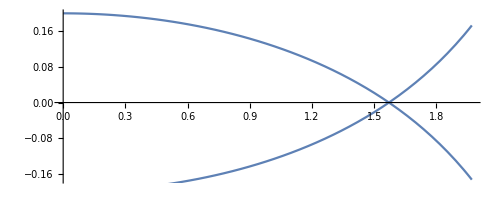

```mathematica
GUdd = GUdd /. {χ->χ[λ], θ -> θ'[λ], φ->φ[λ]};
derivs = {t'[λ], χ'[λ], θ'[λ], φ'[λ]};
geo1 = χ''[λ]+Sum[Part[GUdd, 2, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
geo2 = θ''[λ]+Sum[Part[GUdd, 3, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
geo3 = φ''[λ]+Sum[Part[GUdd, 4, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];

sol1 = NDSolve[{geo1==0, geo2==0, geo3==0, χ[0]==0.2, θ[0]==π/2, φ[0]==π/2, χ'[0]==0, θ'[0]==0, φ'[0]==-1},{χ[λ], θ[λ], φ[λ]}, {λ,0,10} ]
sol2 = NDSolve[{geo1==0, geo2==0, geo3==0, χ[0]==0.2, θ[0]==π/2, φ[0]==-π/2, χ'[0]==0, θ'[0]==0, φ'[0]==1},{χ[λ], θ[λ], φ[λ]}, {λ,0,10} ]
Show[ParametricPlot[Evaluate[{χ[λ]*Cos[φ[λ]], χ[λ]*Sin[φ[λ]]}/.sol1], {λ, 0, 10}], ParametricPlot[Evaluate[{χ[λ]*Cos[φ[λ]], χ[λ]*Sin[φ[λ]]}/.sol2], {λ, 0, 10}],PlotStyle->Orange]
```

For k = -1

```mathematica
xCoord = {t, χ, θ, φ}
g = {{-1, 0, 0, 0},{0, 1, 0, 0}, {0,0, Sinh[χ]^2, 0}, {0, 0,0, Sinh[χ]^2*Sin[θ]^2}}
```

{t,χ,θ,φ}

{{-1,0,0,0},{0,1,0,0},{0,0,Sinh[χ]^2,0},{0,0,0,Sin[θ]^2 Sinh[χ]^2}}

```mathematica
RGtensors[g,xCoord]
```

gdd = (-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | Sinh[χ]^2 | 0
0 | 0 | 0 | Sin[θ]^2 Sinh[χ]^2)

LineElement = -d[t]^2+d[χ]^2+d[θ]^2 Sinh[χ]^2+d[φ]^2 Sin[θ]^2 Sinh[χ]^2

gUU = (-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | Csch[χ]^2 | 0
0 | 0 | 0 | Csc[θ]^2 Csch[χ]^2)

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Einstein computed in 0. sec

All tasks completed in 0.

```mathematica
"Aborted after 0."
```

Aborted after 0.

```mathematica
GUdd
GUdd = GUdd /. {χ->χ[λ], θ -> θ'[λ], φ->φ[λ]};
derivs = {t'[λ], χ'[λ], θ'[λ], φ'[λ]};
geo4= χ''[λ]+Sum[Part[GUdd, 2, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
geo5 = θ''[λ]+Sum[Part[GUdd, 3, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
geo6 = φ''[λ]+Sum[Part[GUdd, 4, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,-Cosh[χ] Sinh[χ],0},{0,0,0,-Cosh[χ] Sin[θ]^2 Sinh[χ]}},{{0,0,0,0},{0,0,Coth[χ],0},{0,Coth[χ],0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,Coth[χ]},{0,0,0,Cot[θ]},{0,Coth[χ],Cot[θ],0}}}

```mathematica
sol3= NDSolve[{geo4==0, geo5==0, geo6==0, χ[0]==0.2, θ[0]==π/2, φ[0]==π/2, χ'[0.2]==0, θ'[0.2]==0, φ'[0]==-1},{χ[λ], θ[λ], φ[λ]}, {λ,0.2,10} ]
sol4 = NDSolve[{geo4==0, geo5==0, geo6==0, χ[0]==0.2, θ[0]==π/2, φ[0]==-π/2, χ'[0.2]==0.1, θ'[0]==0, φ'[0]==1},{χ[λ], θ[λ], φ[λ]}, {λ,0,10} ]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at λ == 0..

NDSolve[{-Cosh[χ[λ]] Sinh[χ[λ]] θ'[λ]^2-Cosh[χ[λ]] Sin[θ'[λ]]^2 Sinh[χ[λ]] φ'[λ]^2+χ''[λ]==0,-Cos[θ'[λ]] Sin[θ'[λ]] φ'[λ]^2+2 Coth[χ[λ]] θ'[λ] χ'[λ]+θ''[λ]==0,2 Cot[θ'[λ]] θ'[λ] φ'[λ]+2 Coth[χ[λ]] φ'[λ] χ'[λ]+φ''[λ]==0,χ[0]==0.2,θ[0]==π/2,φ[0]==π/2,χ'[0.2]==0,θ'[0.2]==0,φ'[0]==-1},{χ[λ],θ[λ],φ[λ]},{λ,0.2,10}]

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at λ == 0..

NDSolve[{-Cosh[χ[λ]] Sinh[χ[λ]] θ'[λ]^2-Cosh[χ[λ]] Sin[θ'[λ]]^2 Sinh[χ[λ]] φ'[λ]^2+χ''[λ]==0,-Cos[θ'[λ]] Sin[θ'[λ]] φ'[λ]^2+2 Coth[χ[λ]] θ'[λ] χ'[λ]+θ''[λ]==0,2 Cot[θ'[λ]] θ'[λ] φ'[λ]+2 Coth[χ[λ]] φ'[λ] χ'[λ]+φ''[λ]==0,χ[0]==0.2,θ[0]==π/2,φ[0]==-π/2,χ'[0.2]==0.1,θ'[0]==0,φ'[0]==1},{χ[λ],θ[λ],φ[λ]},{λ,0,10}]

For k = 0

```mathematica
g = {{-1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, χ^2, 0}, {0, 0, 0, χ^2*Sin[θ]^2}}
```

{{-1,0,0,0},{0,1,0,0},{0,0,χ^2,0},{0,0,0,χ^2 Sin[θ]^2}}

```mathematica
xCoord = {t, χ, θ,φ}
```

{t,χ,θ,φ}

```mathematica
RGtensors[g,xCoord]
```

gdd = (-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | χ^2 | 0
0 | 0 | 0 | χ^2 Sin[θ]^2)

LineElement = -d[t]^2+χ^2 d[θ]^2+d[χ]^2+χ^2 d[φ]^2 Sin[θ]^2

gUU = (-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/χ^2 | 0
0 | 0 | 0 | Csc[θ]^2/χ^2)

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Flat Space!

Aborted after 0.

```mathematica
GUdd
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,-χ,0},{0,0,0,-χ Sin[θ]^2}},{{0,0,0,0},{0,0,1/χ,0},{0,1/χ,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/χ},{0,0,0,Cot[θ]},{0,1/χ,Cot[θ],0}}}

```mathematica
GUdd = GUdd /. {χ->χ[λ], θ -> θ'[λ], φ->φ[λ]};
derivs = {t'[λ], χ'[λ], θ'[λ], φ'[λ]};
geo7= χ''[λ]+Sum[Part[GUdd, 2, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
geo8 = θ''[λ]+Sum[Part[GUdd, 3, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
geo9 = φ''[λ]+Sum[Part[GUdd, 4, i, j]*derivs[[i]]*derivs[[j]], {i, 2, 4}, {j, 2, 4}];
```

```mathematica
sol5 = NDSolve[{geo7==0, geo8==0, geo9==0, χ[0]==0.2, θ[0]==π/2, φ[0]==π/2, χ'[0]==0, θ'[0]==0, φ'[0]==-1},{χ[λ], θ[λ], φ[λ]}, {λ,0,10} ]
sol6 = NDSolve[{geo7==0, geo8==0, geo9==0, χ[0]==0.2, θ[0]==π/2, φ[0]==-π/2, χ'[0]==0, θ'[0]==0, φ'[0]==1},{χ[λ], θ[λ], φ[λ]}, {λ,0,10} ]
```

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at λ == 0..

NDSolve[{-χ[λ] θ'[λ]^2-Sin[θ'[λ]]^2 χ[λ] φ'[λ]^2+χ''[λ]==0,-Cos[θ'[λ]] Sin[θ'[λ]] φ'[λ]^2+(2 θ'[λ] χ'[λ])/χ[λ]+θ''[λ]==0,2 Cot[θ'[λ]] θ'[λ] φ'[λ]+(2 φ'[λ] χ'[λ])/χ[λ]+φ''[λ]==0,χ[0]==0.2,θ[0]==π/2,φ[0]==π/2,χ'[0]==0,θ'[0]==0,φ'[0]==-1},{χ[λ],θ[λ],φ[λ]},{λ,0,10}]

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at λ == 0..

NDSolve[{-χ[λ] θ'[λ]^2-Sin[θ'[λ]]^2 χ[λ] φ'[λ]^2+χ''[λ]==0,-Cos[θ'[λ]] Sin[θ'[λ]] φ'[λ]^2+(2 θ'[λ] χ'[λ])/χ[λ]+θ''[λ]==0,2 Cot[θ'[λ]] θ'[λ] φ'[λ]+(2 φ'[λ] χ'[λ])/χ[λ]+φ''[λ]==0,χ[0]==0.2,θ[0]==π/2,φ[0]==-π/2,χ'[0]==0,θ'[0]==0,φ'[0]==1},{χ[λ],θ[λ],φ[λ]},{λ,0,10}]

```mathematica
Show[ParametricPlot[Evaluate[{χ[λ]*Cos[φ[λ]], χ[λ]*Sin[φ[λ]]}/.sol5], {λ, 0, 10}], ParametricPlot[Evaluate[{χ[λ]*Cos[φ[λ]], χ[λ]*Sin[φ[λ]]}/.sol6], {λ, 0, 10}],PlotStyle->Orange]
```

ReplaceAll::reps: {NDSolve[{-χ[λ] ((«1»)^(«1»)[«1»])^2-Sin[«1»]^2 χ[λ] ((«1»)^(«1»)[«1»])^2+χ''[λ]==0,-Cos[(«1»)^(«1»)[«1»]] Sin[(«1»)^(«1»)[«1»]] ((«1»)^(«1»)[«1»])^2+(2 θ'[λ] χ'[λ])/χ[«1»]+θ''[λ]==0,«5»,θ'[0]==0,φ'[0]==-1},{χ[λ],θ[λ],φ[λ]},{λ,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-χ[0.000204082] ((«1»)^(«1»)[«1»])^2-Sin[«1»]^2 χ[0.000204082] ((«1»)^(«1»)[«1»])^2+χ''[0.000204082]==0,«7»,φ'[0]==-1},{χ[0.000204082],θ[«23»],φ[0.000204082]},{0.000204082,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204082 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-1. χ[0.000204082] ((«1»)^(«1»)[«1»])^2-1. Sin[«1»]^2 χ[0.000204082] ((«1»)^(«1»)[«1»])^2+χ''[0.000204082]==0.,«7»,φ'[0.]==-1.},{χ[0.000204082],θ[«23»],φ[«23»]},{0.000204082,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NDSolve::ndnum: Encountered non-numerical value for a derivative at λ == 0..

-Graphics-

## 4. Perfect Fluid

```mathematica
xCoord = {t, r, θ, φ};
g = {{-1, 0, 0, 0}, 
{0, (a[t])^2/(1-k*r^2),0 , 0}, 
{0, 0, r^2*(a[t])^2 , 0}, 
{0, 0, 0, r^2*(a[t])^2}Sin[θ]^2}
```

{{-1,0,0,0},{0,a[t]^2/(1-k r^2),0,0},{0,0,r^2 a[t]^2,0},{0,0,0,r^2 a[t]^2 Sin[θ]^2}}

```mathematica
RGtensors[g, xCoord]
```

gdd = (-1 | 0 | 0 | 0
0 | a[t]^2/(1-k r^2) | 0 | 0
0 | 0 | r^2 a[t]^2 | 0
0 | 0 | 0 | r^2 a[t]^2 Sin[θ]^2)

LineElement = -(a[t]^2 d[r]^2)/(-1+k r^2)-d[t]^2+r^2 a[t]^2 d[θ]^2+r^2 a[t]^2 d[φ]^2 Sin[θ]^2

gUU = (-1 | 0 | 0 | 0
0 | -(-1+k r^2)/a[t]^2 | 0 | 0
0 | 0 | 1/(r^2 a[t]^2) | 0
0 | 0 | 0 | Csc[θ]^2/(r^2 a[t]^2))

gUU computed in 0. sec

Gamma computed in 0. sec

Riemann(dddd) computed in 0. sec

Riemann(Uddd) computed in 0. sec

Ricci computed in 0. sec

Weyl computed in 0. sec

Conformally Flat

Einstein computed in 0. sec

All tasks completed in 0.

```mathematica
Rdd
```

{{-(3 a''[t])/a[t],0,0,0},{0,-(2 k+2 a'[t]^2+a[t] a''[t])/(-1+k r^2),0,0},{0,0,r^2 (2 k+2 a'[t]^2+a[t] a''[t]),0},{0,0,0,r^2 Sin[θ]^2 (2 k+2 a'[t]^2+a[t] a''[t])}}

```mathematica
R
```

(6 (k+a'[t]^2+a[t] a''[t]))/a[t]^2

```mathematica
FullSimplify[Rdd]
```

{{-(3 a''[t])/a[t],0,0,0},{0,(2 (k+a'[t]^2)+a[t] a''[t])/(1-k r^2),0,0},{0,0,r^2 (2 (k+a'[t]^2)+a[t] a''[t]),0},{0,0,0,r^2 Sin[θ]^2 (2 (k+a'[t]^2)+a[t] a''[t])}}

```mathematica
GUdd
```

{{{0,0,0,0},{0,-(a[t] a'[t])/(-1+k r^2),0,0},{0,0,r^2 a[t] a'[t],0},{0,0,0,r^2 a[t] Sin[θ]^2 a'[t]}},{{0,a'[t]/a[t],0,0},{a'[t]/a[t],-(k r)/(-1+k r^2),0,0},{0,0,r (-1+k r^2),0},{0,0,0,r (-1+k r^2) Sin[θ]^2}},{{0,0,a'[t]/a[t],0},{0,0,1/r,0},{a'[t]/a[t],1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,a'[t]/a[t]},{0,0,0,1/r},{0,0,0,Cot[θ]},{a'[t]/a[t],1/r,Cot[θ],0}}}

```mathematica
EUd
```

{{-(3 (k+a'[t]^2))/a[t]^2,0,0,0},{0,-(k+a'[t]^2+2 a[t] a''[t])/a[t]^2,0,0},{0,0,-(k+a'[t]^2+2 a[t] a''[t])/a[t]^2,0},{0,0,0,-(k+a'[t]^2+2 a[t] a''[t])/a[t]^2}}

```mathematica
R
```

(6 (k+a'[t]^2+a[t] a''[t]))/a[t]^2

```mathematica
Part[Rdd,2,2]
```

-(2 k+2 a'[t]^2+a[t] a''[t])/(-1+k r^2)

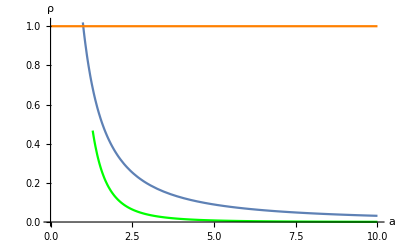

```mathematica
Show[Plot[y[x] =x^(-3/2), {x, 0, 10}, AxesLabel->{a, ρ}],
Plot[y[x] = x^(-3), {x, 0, 10}, PlotStyle->Green],
Plot[y[x] = 1, {x, 0, 10}, PlotStyle->Orange]]
```

## 5. Friedmann Equations

```mathematica
Part[Rdd,2,2]+Part[Rdd,3,3]+Part[Rdd,4,4]
```

r^2 (2 k+2 a'[t]^2+a[t] a''[t])-(2 k+2 a'[t]^2+a[t] a''[t])/(-1+k r^2)+r^2 Sin[θ]^2 (2 k+2 a'[t]^2+a[t] a''[t])

```mathematica
lhs = FullSimplify[Part[Rdd,2,2]+Part[Rdd,3,3]+Part[Rdd,4,4]]
```

(r^2+1/(1-k r^2)+r^2 Sin[θ]^2) (2 (k+a'[t]^2)+a[t] a''[t])

```mathematica
rhs = FullSimplify[Part[gdd,2,2]+Part[gdd,3,3]+Part[gdd,4,4]]
```

a[t]^2 (r^2+1/(1-k r^2)+r^2 Sin[θ]^2)

```mathematica
lhs
```

(r^2+1/(1-k r^2)+r^2 Sin[θ]^2) (2 (k+a'[t]^2)+a[t] a''[t])

```mathematica
rhs
```

a[t]^2 (r^2+1/(1-k r^2)+r^2 Sin[θ]^2)

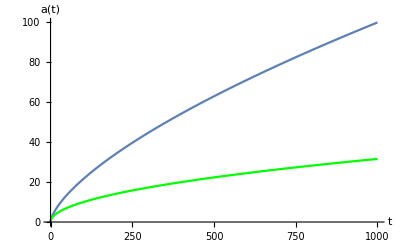

```mathematica
Show[Plot[y[x] =x^(2/3), {x, 0, 1000}, AxesLabel->{t, a[t]}],
Plot[y[x] = x^(1/2), {x, 0, 1000}, PlotStyle->Green]]
```

```mathematica
_□
```

Failure[…]_□